```mathematica
(*
	Questa funzione disegna un grafo di Levi.

   INPUT:   cx     Coordinata X del centro del grafo (default 0)
		  tipo   Tipo grafo (0=Don't care,1=Fano,2=Tutte-Coxeter) (default 1)
		  prm    Permutazione degli n nodi (default la permutazione identica)
		  nfs    Rotazione del grafo. Viene realizzata una rotazione in senso antiorario di angolo nsf*(360/n gradi)
		         Se nfs e' intero questo corrisponde ad una rotazione dei nodi. (default 0)
		  nn     Numero di nodi del grafo (numero pari) (default 4)
          lagg   Lista connessioni interne di n nodi (default nessun nodo)
		  sgl    Sigle nodi elementi (default {1,2,3,4,...})
	      
	      
OUTPUT:  Lista elementi da graficare
     
*)
genLevi[cx_:0,tipo_:1,prm_:{0},nfs_:0,nn_:4,lagg_:{{0}},sgl_:{0}]:=(
If[tipo==0,
n=nn;
];
If[tipo==1,
n=14;
];
If[tipo==2,
n=30;
];

If[tipo==0,
lpagg=lagg;
];
If[tipo==1,
lpagg={{10},{7},{12},{9},{14},{11},{2},{13},{4},{1},{6},{3},{8},{5}};
];
If[tipo==2,
lpagg={{14},{19},{24},{11},{28},{15},{20},{25},{30},{17},{4},{21},{26},{1},{6},{23},{10},{27},{2},{7},{12},{29},{16},{3},{8},{13},{18},{5},{22},{9}};
];

If[tipo==2,
sigle={12,13,14,15,16,23,24,25,26,34,35,36,45,46,56},
If[sgl[[1]]==0,
sigle=Range[n],
sigle=sgl;
];
];

If[prm[[1]]==0,
perm=Range[n],
perm=prm;
];

lcoo=Range[n];
dxy=Range[n];

clr1=Black;
clr2=Green;

cy=0;
r=10;

stepa=Pi/n;
da=2stepa;
ang=Pi/2+stepa+nfs da;

For[k=1,k≤n,k++,
dxy[[perm[[k]]]]={Cos[ang],Sin[ang]};
ang-=da;
];

For[k=1,k≤n,k++,
lcoo[[k]]={cx+r dxy[[k]][[1]],cy+r dxy[[k]][[2]]};
ang-=da;
];

colors={"Red","Blue"};

p=Range[n];
sizep=10;
offs=2;

For[k=1,k≤n,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[sigle[[Floor[k/2]+1]],lcoo[[k]]+offs dxy[[k]]]};
];

For[k=2,k≤n,k+=2,
p[[k]]={AbsolutePointSize[sizep],RGBColor[colors[[Mod[k-1,2]+1]]],Point[lcoo[[k]]],Text[sigle[[Mod[Floor[(k-2)/2],n/2]+1]],lcoo[[k]]+offs dxy[[k]]],Text[sigle[[Mod[Floor[k/2],n/2]+1]],lcoo[[k]]+2offs dxy[[k]]]};If[lpagg[[1]][[1]]≠ 0,
For[l=1,l≤Length[ lpagg[[k]]],l++,
AppendTo[p[[k]],{Text[sigle[[Floor[lpagg[[k]][[l]]/2+1]]],lcoo[[k]]+(l+2)offs dxy[[k]]]}];
];
];
];

ln=Range[n];

For[k=1,k<n,k++,
ln[[k]]=Line[{lcoo[[k]],lcoo[[k+1]]}];
];
ln[[n]]=Line[{lcoo[[n]],lcoo[[1]]}];

If[lpagg[[1]][[1]]==0,
Return[{p,{clr1,ln}}],
lnaus=Range[n];
For[k=1,k≤n,k++,lnaus[[k]]={};
For[l=1,l≤Length[lpagg[[k]]],l++,
AppendTo[lnaus[[k]],Line[{lcoo[[k]],lcoo[[lpagg[[k]][[l]]]]}]];
];
];
];

Return[{p,{clr1,ln},{clr2,lnaus}}];
)

(*
	Questa funzione applica una serie di trasposizioni ad una permutazione di partenza

	INPUT: per insieme delle trasposizioni da applicare
		 n   numero di elementi della permutazione di partenza
		 prm permutazione di partenza (default la permutazione identica su n elementi)
*)
genPerm[per_,n_,prm_:{0}]:=(
If[prm[[1]]==0,
result=Range[n],
result=prm;
];
nel1=Length[per];
For[k1=1,k1≤nel1,k1++,
nel2=Length[per[[k1]]];
For[k2=nel2,k2>=1,k2--,
inda=per[[k1]][[k2]];
If[k2<nel2,
result[[indp]]=result[[inda]],
appo=result[[inda]];
];
indp=inda;
];
result[[indp]]=appo;
];
Return[result];
)

(*
	Questa funzione applica una riflessione ad una permutazione iniziale di vertici
   La riflessione e' effettuata rispetto ad un asse che passa per il vertice v1
   se v1=v2 o passa per la mediana del lato che congiunge v1 a v2 (dovra' essere v2=(v1+1 modulo n) 

	INPUT: v1  primo vertice
		 v2  secondo vertice
		 n   numero dei vertici
		 prm permutazione iniziale di n vertici
*)
genRiflex[v1_,v2_,n_,prm_:{0}]:=(
If[prm[[1]]==0,
result=Range[n],
result=prm;
];
If[v1==v2,
v=v1;
For[k=1,k≤Floor[(n-1)/2],k++,
appo=result[[Mod[v-1-k,n]+1]];
result[[Mod[v-1-k,n]+1]]=result[[Mod[v-1+k,n]+1]];
result[[Mod[v-1+k,n]+1]]=appo;
],
For[k=1,k≤Floor[n/2],k++,
appo=result[[Mod[v1-k,n]+1]];
result[[Mod[v1-k,n]+1]]=result[[Mod[v2+k-2,n]+1]];
result[[Mod[v2+k-2,n]+1]]=appo;
];
];
Return[result];
)
```

```mathematica
gen1={{5,11},{6, 10},{7, 17},{8 ,16},{9, 15},{12, 28},{13, 29},{14, 30},{18, 20},{21, 27},{22, 26},{23 ,25}};
gen2={{5,11},{6, 12},{7, 21},{8 ,22},{9, 29},{10, 28},{13, 15},{16, 26},{17, 27},{23, 25}};
gen3={{2,14},{3, 15},{4, 6},{7 ,11},{8, 10},{12, 20},{13, 19},{16, 24},{17, 25},{18, 26}};
gen4={{1,2,3, 4,5, 6,7 ,8,9, 30},{10, 29,14, 19,24, 11,28, 15,20, 25},{12, 27,16 ,21,26,17,22,13,18,23}};

g1=genLevi[0,2];
g2=genLevi[35,2,genPerm[gen1,30]];
g3=genLevi[70,2,genPerm[gen2],30];
g4=genLevi[105,2,genPerm[gen3],30];
g5=genLevi[140,2,genPerm[gen4],30];
Graphics[{g1,g2,g3,g4,g5}]
```

```mathematica
gen1={{5,9},{6,8},{10,14},{11,13}};
gen2={{4,12},{5,11},{9,13},{10,14}};
gen3={{2,14},{3,5},{6,12},{7,13}};
gen4={{1,3},{4,14},{9,13},{10,12}};

g1=genLevi[0];
g2=genLevi[35,1,genPerm[gen1,14]];
g3=genLevi[70,1,genPerm[gen2,14]];
g4=genLevi[105,1,genPerm[gen3,14]];
g5=genLevi[140,1,genPerm[gen4,14]];
Graphics[{g1,g2,g3,g4,g5}]
```

```mathematica
Graphics[genLevi[0,0,{0}]]
```

```mathematica
gen1={{4,14},{5,37},{6,42},{7,29},{8,16},{9,39},{10,26},{13,17},{15,25},{18,34},{27,33},{28,38},{35,41},{36,40}};
gen2={{2,12},{3,11},{4,26},{5,35},{9,13},{10,14},{17,39},{18,38},{19,23},{20,22},{27,33},{28,34},{36,40},{37,41}};
gen3={{1,7},{2,38},{3,37},{4,36},{5,35},{8,32},{9,33},{11,41},{12,18},{13,27},{19,23},{20,22},{25,31},{26,40},{28,34},{30,42}};
gen4={{1,9},{4,30},{5,11},{6,10},{7,33},{8,32},{12,28},{13,27},{17,29},{18,34},{25,31},{26,40},{35,41},{36,42}};

g1=genLevi[0,0,{0},0,42,{{6,12,32},{9,19,39},{3},{17,25,33},{5},{1,15,35},{7},{13,21,25},{9},{15,33,41},{11},{1,17,23},{13},{3,27,37},{15},{21,29,39},{17},{7,27,41},{19},{3,35,41},{21},{5,11,37},{23},{15,19,31},{25},{11,35,39},{27},{5,9,23},{29},{3,7,11},{31},{1,21,27},{33},{13,19,29},{35},{9,17,31},{37},{7,23,33},{39},{5,13,31},{41},{25,29,37}},{0}];
g2=genLevi[45,0,genPerm[gen1,42],0,42,{{6,12,32},{9,19,39},{3},{17,25,33},{5},{1,15,35},{7},{13,21,25},{9},{15,33,41},{11},{1,17,23},{13},{3,27,37},{15},{21,29,39},{17},{7,27,41},{19},{3,35,41},{21},{5,11,37},{23},{15,19,31},{25},{11,35,39},{27},{5,9,23},{29},{3,7,11},{31},{1,21,27},{33},{13,19,29},{35},{9,17,31},{37},{7,23,33},{39},{5,13,31},{41},{25,29,37}},{0}];
g3=genLevi[90,0,genPerm[gen2,42],0,42,{{6,12,32},{9,19,39},{3},{17,25,33},{5},{1,15,35},{7},{13,21,25},{9},{15,33,41},{11},{1,17,23},{13},{3,27,37},{15},{21,29,39},{17},{7,27,41},{19},{3,35,41},{21},{5,11,37},{23},{15,19,31},{25},{11,35,39},{27},{5,9,23},{29},{3,7,11},{31},{1,21,27},{33},{13,19,29},{35},{9,17,31},{37},{7,23,33},{39},{5,13,31},{41},{25,29,37}},{0}];
g4=genLevi[135,0,genPerm[gen3,42],0,42,{{6,12,32},{9,19,39},{3},{17,25,33},{5},{1,15,35},{7},{13,21,25},{9},{15,33,41},{11},{1,17,23},{13},{3,27,37},{15},{21,29,39},{17},{7,27,41},{19},{3,35,41},{21},{5,11,37},{23},{15,19,31},{25},{11,35,39},{27},{5,9,23},{29},{3,7,11},{31},{1,21,27},{33},{13,19,29},{35},{9,17,31},{37},{7,23,33},{39},{5,13,31},{41},{25,29,37}},{0}];
g5=genLevi[180,0,genPerm[gen4,42],0,42,{{6,12,32},{9,19,39},{3},{17,25,33},{5},{1,15,35},{7},{13,21,25},{9},{15,33,41},{11},{1,17,23},{13},{3,27,37},{15},{21,29,39},{17},{7,27,41},{19},{3,35,41},{21},{5,11,37},{23},{15,19,31},{25},{11,35,39},{27},{5,9,23},{29},{3,7,11},{31},{1,21,27},{33},{13,19,29},{35},{9,17,31},{37},{7,23,33},{39},{5,13,31},{41},{25,29,37}},{0}];
Graphics[{g1,g2,g3,g4,g5}]
```

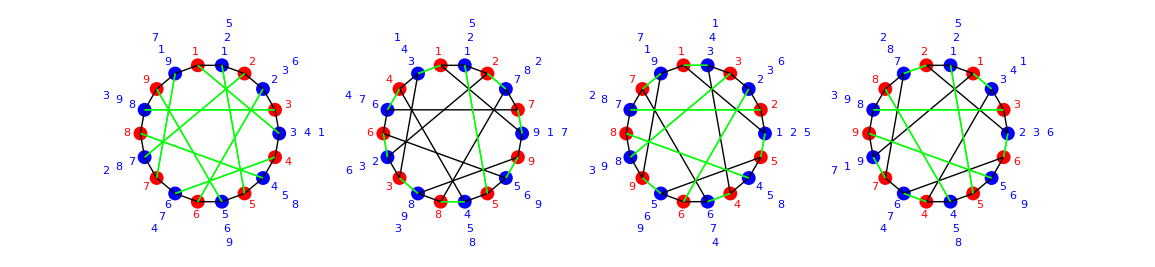

```mathematica
gen1={{4,14},{5,13},{6,18},{7,17},{8,10},{11,15},{12,16}};
gen2={{2,6},{3,5},{7,9},{10,12},{13,17},{14,16}};
gen3={{1,3},{4,6},{7,11},{8,10},{14,18},{15,17}};
g1=genLevi[0,0,{0},0,18,{{6},{9},{14},{11},{16},{1},{12},{15},{2},{17},{4},{7},{18},{3},{8},{5},{10},{13}},{0}];
g2=genLevi[35,0,genPerm[gen1,18],0,18,{{6},{9},{14},{11},{16},{1},{12},{15},{2},{17},{4},{7},{18},{3},{8},{5},{10},{13}},{0}];
g3=genLevi[70,0,genPerm[gen2,18],0,18,{{6},{9},{14},{11},{16},{1},{12},{15},{2},{17},{4},{7},{18},{3},{8},{5},{10},{13}},{0}];
g4=genLevi[105,0,genPerm[gen3,18],0,18,{{6},{9},{14},{11},{16},{1},{12},{15},{2},{17},{4},{7},{18},{3},{8},{5},{10},{13}},{0}];
Graphics[{g1,g2,g3,g4}]
```